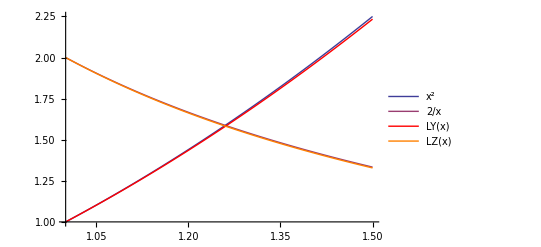

Погрешность приближения функции y[x] равна: 0.0033938

Погрешность приближения функции z[x] равна: 0.00188955

```mathematica
(*Зададим правые части системы дифференциальных уравнений*)
f1[x_,y_,z_]=y*z;
f2[x_,y_,z_]=-z^2+z/x;
(*Зададим начальные условия*)
x0=1;
Y={1};
Z={2};
(*Зададим правый конец отрезка, на котором ищется решение*)
b=1.5;
(*Зададим количество частичных отрезков*)
n=30;
(*Найдём шаг разбиения*)
h=(b-x0)/n;
(*Построим разбиение отрезка на частичные*)
X=Table[x0+k*h,{k,0,n}];
(*Реализуем алгоритм метода Эйлера решения задачи Коши для систем дифференциальных уравнений*)
For[k=1,k≤n,k++,
AppendTo[Y,Y[[k]]+h*f1[X[[k]],Y[[k]],Z[[k]]]];
AppendTo[Z,Z[[k]]+h*f2[X[[k]],Y[[k]],Z[[k]]]]
];
(*Выполним интерполяцию найденного приближенного решения*)LY[x_]=Sum[Y[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
LZ[x_]=Sum[Z[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
(*Найдем точное решение данной задачи Коши*)
DSol=DSolve[{y'[x]==f1[x,y[x],z[x]],z'[x]==f2[x,y[x],z[x]],y[x0]==Y[[1]],z[x0]==Z[[1]]},{y[x],z[x]},x];
Sol={y[x]/.DSol[[1,2]],z[x]/.DSol[[1,1]]};
(*Построим графики точного и приближенного решения в одной системе координат*)
GL=Plot[{LY[x],LZ[x]},{x,x0,b},PlotStyle->{Red,Orange},PlotLegends->"Expressions"];
G=Plot[Sol,{x,x0,b},PlotLegends->"Expressions"];
Show[G,GL]
(*Найдем погрешность приближения*)
ry=NIntegrate[Abs[LY[x]-Sol[[1]]],{x,x0,b}];
rz=NIntegrate[Abs[LZ[x]-Sol[[2]]],{x,x0,b}];
Print["Погрешность приближения функции y[x] равна: ",ry]
Print["Погрешность приближения функции z[x] равна: ",rz]
```